### Predict

Predict is a function that works on variety of data types and output a PredictorFunction. It predicts a value from the given data. The format for data is rule based array {data -> target}. The target need to be a numerical value. It automatically selects a machine learning model based on the type of data. But we can also specify method of our own choosing using Method->” “.

```mathematica
pd = Predict[{1.11->1,2.22->2,3.33->3,4.44->4,4.44->5}]
```

PredictorFunction[…]

```mathematica
pd[3.7]
```

3.61515

Getting the Regression line.

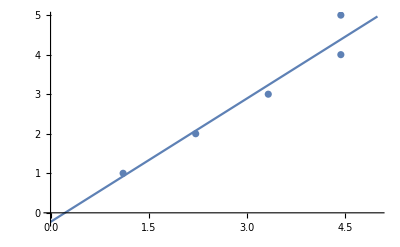

```mathematica
Show[Plot[pd[x],{x,0,5},Exclusions->None],ListPlot[List@@@{1.11->1,2.22->2,3.33->3,4.44->4,4.44->5}]]
```

We can also get information about PredictorFunction, just as we did in classify.

```mathematica
PredictorInformation[pd]
```

Predictor information
Method | Linear regression
Number of features | 1
Number of training examples | 5
L1 regularization coefficient | 0
L2 regularization coefficient | 0.1

```mathematica
ExampleData[{"MachineLearning","Titanic"},"Description"]
```

Classify whether a passenger on board the maiden voyage of the RMS Titanic in 1912 survived given their age, sex and class.

```mathematica
titanic = ExampleData[{"MachineLearning","Titanic"},"Data"]
```

{{1st,29.,female}→survived,{1st,0.9167,male}→survived,{1st,2.,female}→died,{1st,30.,male}→died,{1st,25.,female}→died,{1st,48.,male}→survived,{1st,63.,female}→survived,{1st,39.,male}→died,{1st,53.,female}→survived,{1st,71.,male}→died,1289,{3rd,27.,male}→died,{3rd,15.,female}→survived,{3rd,45.5,male}→died,{3rd,Missing[],male}→died,{3rd,Missing[],male}→died,{3rd,14.5,female}→died,{3rd,Missing[],female}→died,{3rd,26.5,male}→died,{3rd,27.,male}→died,{3rd,29.,male}→died}
 |  |  |  |